# Social Network Analysis

## Chen Avin School of Electrical and Computer Engineering

# Unit 7 Community Detection

(Based on Networks: An Introduction. By M.E.J Newman)

## Last Time

Core-Periphery

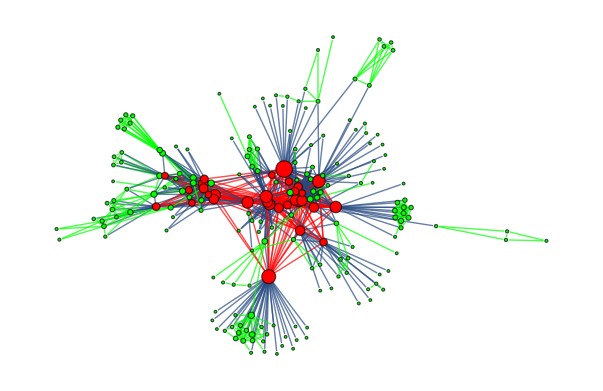

## Group of Vertices

Cliques

k-plex - A k-plex is a maximal set of vertices such that each vertex is adjacent to all except k others.

k-clique - A k-clique is a maximal set of vertices that are at a distance no greater than k from each other (using outside).

k-club - A k-club is a maximal set of vertices where the diameter of the corresponding subgraph is at most k (path is inside the group)

## Finally... We get to use our Facebook class networks

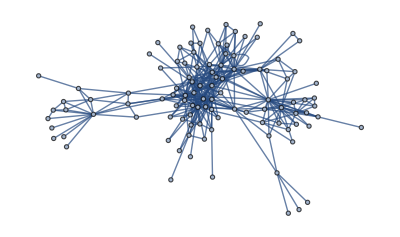

```mathematica
SetDirectory[NotebookDirectory[]];
file = Rest[Import["data/stormofswords.csv"]];
tribes = Import["data/tribes.csv"];
nodes =Flatten[tribes[[All,1]]];
edges =#[[1]]<->#[[2]]&/@ file [[All,{1,2}]];
ThronesG =Graph[nodes,edges, VertexLabels->Placed["Name",Tooltip]]
```

## k - plex

k-plex - A k-plex is a maximal set of vertices such that each vertex is adjacent to all except k others.

```mathematica
FindKPlex[ThronesG,1]
```

{{Cersei,Gregor,Ilyn,Joffrey,Meryn,Sandor,Tyrion}}

```mathematica
Manipulate[Column[{HighlightGraph[ThronesG,SG =Subgraph[ThronesG,FindKPlex[ThronesG,i],VertexLabels->Placed["Name",Tooltip]]],"Number of Thrones: "<>ToString[ VertexCount[SG]],"Min Degree: "<>ToString[ Min[VertexDegree[SG]]],SG}],{{i,1,"k-Plex"},1,20,1}]
```

## k - clique

k-clique - A k-clique is a maximal set of vertices that are at a distance no greater than k from each other (using out side).

```mathematica
Manipulate[Column[{HighlightGraph[ThronesG,SG =Subgraph[ThronesG,FindKClique[ThronesG,i],VertexLabels->Placed["Name",Tooltip]]],"Number of Thrones: "<>ToString[ VertexCount[SG]],"Min Degree: "<>ToString[ Min[VertexDegree[SG]]],SG}],{{i,1,"k-clique"},1,20,1}]
```

## k - club

k-club - A k-club is a maximal set of vertices where the diameter of the corresponding subgraph is at most k (path is inside the group)

```mathematica
Manipulate[Column[{HighlightGraph[ThronesG,SG =Subgraph[ThronesG,FindKClub[ThronesG,i],VertexLabels->Placed["Name",Tooltip]]],"Number of Thrones: "<>ToString[ VertexCount[SG]],"Min Degree: "<>ToString[ Min[VertexDegree[SG]]],SG}],{{i,1,"k-club"},1,20,1}]
```

## k-core

k-core - A k-core component is a maximal weakly connected subgraph in which all vertices have degree at least k

Easy to find, just remove node iteratively

```mathematica
Manipulate[Column[{HighlightGraph[ThronesG,SG =Subgraph[ThronesG,KCoreComponents[ThronesG,i]]],"Number of Students: "<>ToString[ VertexCount[SG]],"Min Degree: "<>ToString[ Min[VertexDegree[SG]]],SG}],{{i,0,"k-core"},0,20,1}]
```

## Graph Partitioning and Community Detection

Divide the network into groups, clusters or communities according to edges (graph topology)

Graph Partitioning is a classic (hard) problem

Both are important to understand the graph structure, processes on the graph (like diffusion) and for efficient parallel computation

Basic guideline: minimize the edges between groups

The difference between  Graph Partitioning and Community Detection:

are the number and/or the size of the group is given?

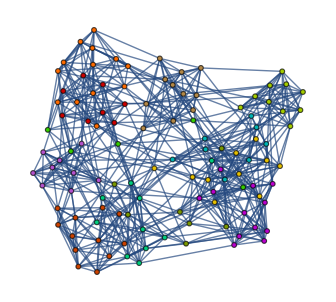
-Graphics--Graphics-

## Graph Partitioning

Consider the “simple” case - partition the graph into two equal groups with minimum cut

Why is it hard?

Known to be NP-hard, Also hard to approximate

## Kernighan-Lin Algorithm

Simple and one of the best known heuristic algorithm

“Vertex Moving” approach

Start from any partition (say, equal size partition)

Find the best pair to “switch” (in hope to reduce the cut)

Repeat of remaining nodes until no more nodes to “switch” (in this round)

Pick the best partition you have found in the round and start a new round.

Go until no improvements between rounds

-Graphics--Graphics-

Problem: it is slow, O(n^3) for a round

Pseudocode

-Graphics-= External cost of edge from a- Internal cost of edge from a

-Graphics-

## Spectral Partitioning

Consider Bisection (two equal parts)

G(V,E), n=|V|, m=|E|, two groups: 1, 2

The Number of edges between the two groups

(1) R=1/2(∑A_ij)_(i,j in
different 
groups)

Let s_i present the division of the network

(2) s_i=Piecewise[{{+1, if vertex i belongs to group 1}, {-1, if vertex i belongs to group 2}}]

Then

(3) 1/2(1-s_i s_j)=Piecewise[{{1, if  i and j are in different groups}, {0, if  i and j are in the same groups}}]

So we can rewrite

(4) R=1/4∑_(i,j) A_ij(1-s_i s_j)

Notice that (where k_i is the degree of i, and δ is the Kronecker delta function)

(5) ∑_(i,j) A_ij=∑_i k_i= ∑_i k_i s_i^2=∑_(i,j) k_i δ_ij s_i s_j

Putting back to (4) we get

(6) R=1/4∑_(i,j) (k_i δ_ij-A_ij)s_i s_j=1/4∑_(i,j) L_ij s_i s_j

L is the Laplacian matrix

This is a fundamental matrix with many uses to study graphs

Has the degree k_i on the diagonal and -1 for each edge (where A_ij=1). The sum of each row is then 0.

L_ij=k_i δ_ij-A_ij

L_ij = Piecewise[{{k_i, if i=j}, {-1, if i≠ j and there is an edge (i,j)}, {0, otherwise}}]

L=D-A  (where D is diagonal matrix with degrees along diagonal)

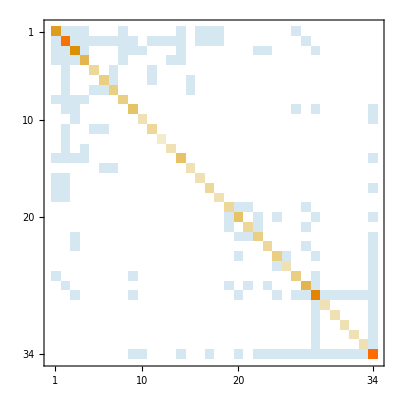

Note that

L·1=0

So (1,1,1,1,.....) is an eigenvector of L and λ_1=0 is an eigen value of L (and all λ_i ≥ 0)

So in a matrix form we can write (6)

(7) R=1/4 s^T Ls

## Our goal is to Minimize R (by setting s)

(7) R=1/4 s^T Ls

To minimize R we need to take a derivative, but the constrains on s (±1) make it hard to find

This lead to the relaxation method: relax some of the constrains

We can relax the ±1 constrain to be

(8) ∑_i s_i^2=n

But we keep the constrain that we want two groups of sizes n_1,n_2

(9) ∑_i s_i=n_1-n_2

In Vector notation

(10) 1^T s = n_1-n_2

Solving (7) using the two constrains (8), (9) is now a standard algebra using Lagrange multiplier (which we denote λ and 2μ)

(11) ∂/(∂s_i)(∑_(i,j) L_ij s_i s_j+λ(n-∑_i s_i^2)+2μ((n_1-n_2)-∑_i s_i))=0

and we get

(12) ∑_j L_ij s_j=λs_i+μ

and in matrix form

(13) Ls=λs+μ1

Using L·1=0 and (10) and multiply (13) and the left with 1^T we get

(14) 1^T Ls=λ1^T s+μ1^T 1 ⟹
0=λ(n_1-n_2)+μn

(15)μ=-λ(n_1-n_2)/n

If we define a new vector

(16)x = s +μ/λ 1= s-(n_1-n_2)/n 1

And finally (13) tell us

(17) Lx=L(s +μ/λ 1)=Ls=λs+μ1= λx

So x  is an eigenvector of L  with eigenvalue λ!!!

Which one we should take? The one that gives the smallest cut size (R)

Notice that 1^Tx =0 (check at home) so x is ortogonal to 1 and therefore the eigenvector vector (1,1,1,1,1...) is out of question (which goes with eigenvalue λ_1=0).

To minimize R we note (check s^T Lx)

(18) R =1/4 s^T Ls = 1/4 x^T Lx = 1/4 λx^T x

Since x^T x = (n_1 n_2)/n (check home)

(19) R =(n_1 n_2)/n λ

So clearly we need to select the smallest eigen value (that is not 0) usually, λ_2 and let v_2 be the corresponding eigenvector

To finalize the selection we need to take the n_1 (or n_2) nodes correspond to the n_1 largest values of v_2

At the end, very simple solution and algorithm

find the eigenvector v_2 correspond to the second smallest eigenvalue of the graph Laplacian

Sort the elements in v_2, compare two possible cuts (first n_1 or first n_2 are in group 1).

Take the best cut

## Example :-)

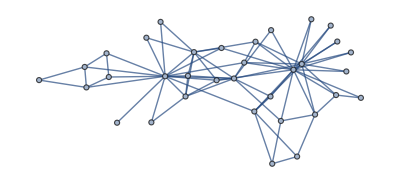

```mathematica
Karate = Graph[ExampleData[{"NetworkGraph","ZacharyKarateClub"}],VertexLabels->Placed["Name",Tooltip]]
```

The “True” Split

```mathematica
KarateClub1 = {3,4,14,2,1,8,22,20,18,13,12,7,17,6,5,11};
```

```mathematica
KarateClub2 = Complement[VertexList[Karate],KarateClub1];
```

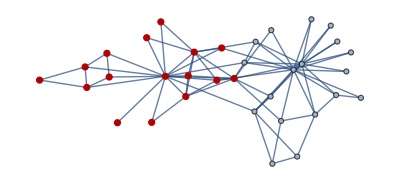

```mathematica
HighlightGraph[Karate,KarateClub1,VertexSize->0.6]
```

Split Sizes

```mathematica
{Length[KarateClub1],Length[KarateClub2]}
```

{16,18}

Laplacian

```mathematica
LapM = KirchhoffMatrix[Karate];
```

```mathematica
MatrixPlot[LapM]
```

-Graphics-

```mathematica
KarateEigenVlaues =Eigenvalues[LapM]//N
```

{18.1367,17.0552,13.3061,10.9211,9.77724,6.9962,6.51554,6.33159,5.61803,5.3786,4.58079,4.48001,4.27588,3.47219,3.38197,3.37615,3.24207,3.01396,2.74916,2.48709,2.,2.,2.,2.,2.,1.95505,1.82606,1.7619,1.59928,1.2594,1.12501,0.909248,0.468525,0.}

```mathematica
KarateEigenVectors =  Eigenvectors[N[LapM]];
```

```mathematica
V2 =N[KarateEigenVectors[[33]]]
```

{0.0412879,0.112137,-0.023219,0.0554998,0.284605,0.323727,0.323727,0.052586,-0.0516013,-0.0928009,0.284605,0.210993,0.109461,0.014742,0.422765,0.100181,0.0136371,0.100181,-0.160963,-0.155695,-0.153026,-0.127664,-0.0951523,-0.16765,-0.18711,-0.0734996,-0.0987534,-0.130345,-0.162751,-0.162751,-0.162751,-0.162751,-0.162751,-0.118903}

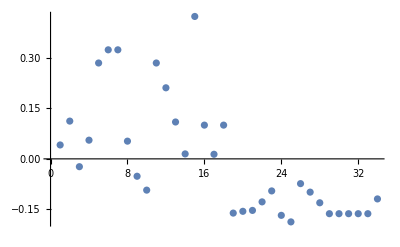

```mathematica
ListPlot[V2]
```

```mathematica
Manipulate[Column[{HighlightGraph[Graph[Karate,VertexStyle->Table[VertexList[Karate][[i]]-> GrayLevel[Rescale[V2][[i]]],{i,1,VertexCount[Karate]}],VertexShapeFunction->Table[VertexList[Karate][[Ordering[V2][[-i]]]]-> "Square",{i,1,j}],VertexSize->0.6],ed =Complement[Complement[EdgeList[Karate],EdgeList[Subgraph[Karate,Complement[VertexList[Karate],VertexList[Karate][[Ordering[V2,-j]]]]]]],EdgeList[Subgraph[Karate,VertexList[Karate][[Ordering[V2,-j]]]]]]],"Cut Size: " <> ToString[Length[ed]]}],{{j,0,"n_1"},0,VertexCount[Karate],1}]
```

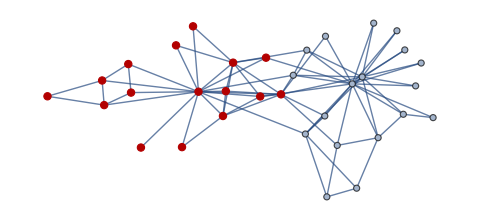

## Community Detection

No input on the community sizes is given

When to stop? minimum cut? ratio cut?

The quality of the cut: Do we see less edges than expected

Minimizing the cut is like maximize the edges with-in groups

A natural candidate is to look for the division with the  highest modularity score (Recall from Homophily)

Modularity Maximization

First simple candidate:

Modularity maximization by vertex moving algorithm

Very similar to Kernighan-Lin Algorithm (initially for 2 groups)

Moving one a vertex (not a swap) that increase the modularity (in a round)

repeat rounds

## Spectral Modularity Maximization

Recall the modularity of the network (the diffrence between number of “homophily” edges to the expected one in random graph).

(20) Q = 1/(2m)∑_ij (A_ij-(k_i k_j)/(2m)) δ(c_i,c_j)

(21) Q = 1/(2m)∑_ij B_ij δ(c_i,c_j)

B_ij =A_ij-(k_i k_j)/(2m)

Note that

(22) ∑_j B_ij =∑_j A_ij-k_i/(2m)∑_j k_j=k_i-k_i/(2m)2m=0

Lets define s as before (for two groups)

(2) s_i=Piecewise[{{+1, if vertex i belongs to group 1}, {-1, if vertex i belongs to group 2}}]

And again

(3)δ(c_i,c_j)= 1/2(s_i s_j+1)=Piecewise[{{0, i ,j are in different groups}, {1, i , j are in the same groups}}]

We can write (21)

(23) Q = 1/(4m)∑_ij B_ij (s_i s_j+1)=1/(4m)∑_ij B_ij s_i s_j

And we have the matrix form

(24) Q = 1/(4m)s^T Bs

Where B is the modularity matrix and now we have a maximization problem

Few more steps, taking the derivative... like before we find that using the relaxtion method

(8) ∑_i s_i^2=n

We note that the solution is the largest eigenvector and the split is according to the sign of the vector elements

All positive elements in the eigenvector are in group 1 and all negative are in group 2

## Another Example

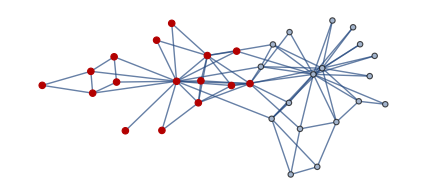

```mathematica
HighlightGraph[Karate,KarateClub1,VertexSize->0.6]
```

```mathematica
ModularityMatrix[G_]:=
Table[Table[AdjacencyMatrix[G][[i,j]]-VertexDegree[G][[i]]VertexDegree[G][[j]]/(2VertexCount[G]),{i,1,VertexCount[G]}],{j,1,VertexCount[G]}]
```

```mathematica
MM = ModularityMatrix[Karate];
```

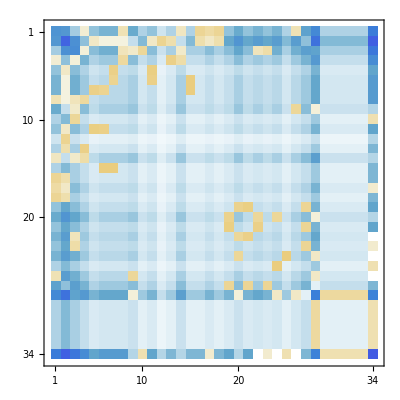

```mathematica
MatrixPlot[MM]
```

```mathematica
MMEV =N[Eigenvalues[MM]];
```

```mathematica
MMEV
```

{-12.6002,4.97708,-3.46764,-3.26714,2.9947,-2.93863,-2.43275,2.31542,-2.09044,-2.,-1.6874,1.48711,1.4557,-1.42928,-1.19235,1.08329,1.03146,-1.02363,0.835289,-0.792199,0.616025,0.41973,-0.417146,0.299473,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Ordering[MMEV,1,Greater]
```

{2}

```mathematica
MMEVec =Eigenvectors[N[MM]];
```

```mathematica
V1= MMEVec[[First@Ordering[MMEV,1,Greater]]]
```

{0.26946,0.387435,0.131782,0.253372,0.133986,0.145725,0.145725,0.209293,-0.054561,-0.0478926,0.133986,0.0778248,0.128713,0.134942,0.0585203,0.131946,0.0575945,0.131946,-0.0754138,-0.216795,-0.0563435,-0.10281,-0.0683889,-0.20634,-0.115828,-0.0963309,-0.101917,-0.324008,-0.13947,-0.13947,-0.13947,-0.13947,-0.13947,-0.369957}

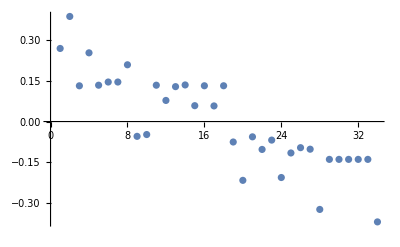

```mathematica
ListPlot[V1]
```

```mathematica
group1 =Flatten[Position[V1,n_ /; n>0]]
```

{1,2,3,4,5,6,7,8,11,12,13,14,15,16,17,18}

```mathematica
group2 = Complement[VertexList[Karate],group1]
```

{9,10,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34}

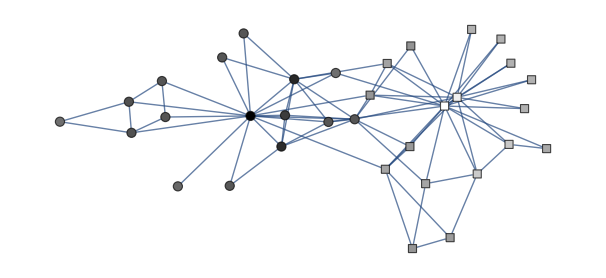

```mathematica
Graph[Karate,VertexStyle->Table[VertexList[Karate][[i]]-> GrayLevel[1-Rescale[V1][[i]]],{i,1,VertexCount[Karate]}],VertexShapeFunction->Table[VertexList[Karate][[group2[[i]]]]-> "Square",{i,1,Length[group2]}],VertexSize->0.6]
```

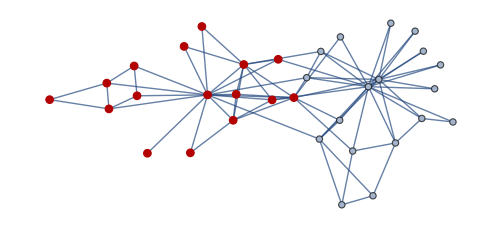

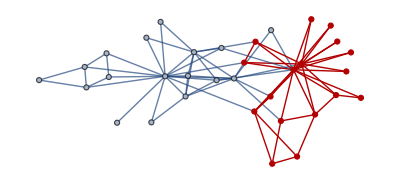

```mathematica
HighlightGraph[Karate,Subgraph[Karate,FindGraphCommunities[Karate,Method->"Modularity"][[1]]]]
```

## Network of Thrones

```mathematica
Length[FindGraphCommunities[ThronesG,Method->"Modularity"]]
```

5

```mathematica
options ={"Modularity","Centrality","CliquePercolation","Hierarchical","Spectral","VertexMoving"};
```

```mathematica
Column[{CommunityGraphPlot[ThronesG,FindGraphCommunities[ThronesG,Method->#]],#}]&/@ options
```

{-Graphics-
Modularity,-Graphics-
Centrality,-Graphics-
CliquePercolation,-Graphics-
Hierarchical,-Graphics-
Spectral,-Graphics-
VertexMoving}

## Football Network

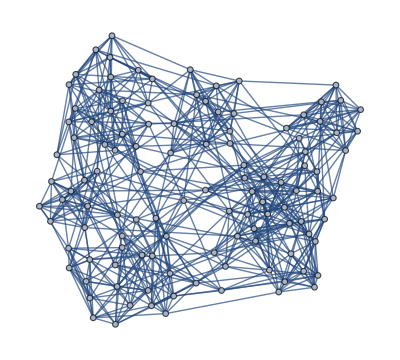

```mathematica
FootBall = Graph[ExampleData[{"NetworkGraph","AmericanCollegeFootball"}],VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
VertexConference =PropertyValue[{FootBall,#},"Conference"]&/@ VertexList[FootBall] ;
```

```mathematica
Tally[VertexConference]
```

{{Big East,8},{Western Athletic,10},{Atlantic Coast,9},{Mid-American,13},{Sun Belt,7},{Big Ten,11},{Mountain West,8},{Pacific Ten,10},{Big Twelve,12},{Conference USA,10},{Southeastern,12},{Independents,5}}

```mathematica
Conference =DeleteDuplicates[VertexConference]
```

{Big East,Western Athletic,Atlantic Coast,Mid-American,Sun Belt,Big Ten,Mountain West,Pacific Ten,Big Twelve,Conference USA,Southeastern,Independents}

```mathematica
Length[Conference]
```

12

```mathematica
BallCommunities =VertexList[FootBall][[Flatten[Position[VertexConference,#]]]]&/@Conference;
```

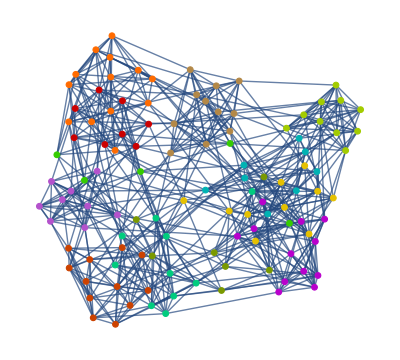

```mathematica
HighlightGraph[FootBall,BallCommunities]
```

```mathematica
CommunityGraphPlot[FootBall,BallCommunities,PlotLegends->Conference]
```

-Graphics-

```mathematica
Column[{CommunityGraphPlot[FootBall,cg =FindGraphCommunities[FootBall,Method->#]],#,"Communities: "<> ToString[Length[cg]]}]&/@ options
```

{-Graphics-
Modularity
Communities: 7,-Graphics-
Centrality
Communities: 10,-Graphics-
CliquePercolation
Communities: 4,-Graphics-
Hierarchical
Communities: 9,-Graphics-
Spectral
Communities: 14,-Graphics-
VertexMoving
Communities: 7}

## Edge Betweenness Algorithm

Use edge Betweenness to split the graph

```mathematica
TopEdgeBetweennessCentrality[g_]:=EdgeList[g][[Ordering[EdgeBetweennessCentrality[g],-1]]]
```

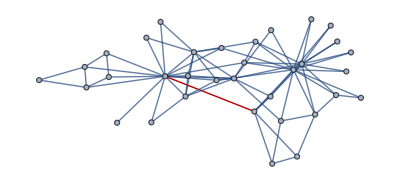

```mathematica
HighlightGraph[Karate,TopEdgeBetweennessCentrality[Karate]]
```

```mathematica
K1= EdgeDelete[Karate,TopEdgeBetweennessCentrality[Karate]];
```

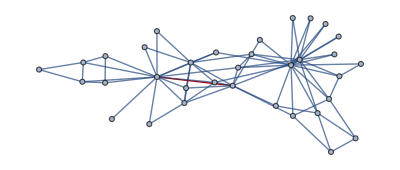

```mathematica
HighlightGraph[K1,TopEdgeBetweennessCentrality[K1]]
```

```mathematica
NextBetweennessEdge[g_,i_]:=Module[{graph=g,list={}},
For[j=1,j≤i,j++,
list=Union[list,TopEdgeBetweennessCentrality[graph]];
graph= EdgeDelete[graph,TopEdgeBetweennessCentrality[graph]];];
list]
```

```mathematica
Manipulate[HighlightGraph[Karate,Style[NextBetweennessEdge[Karate,i],Red,Thickness[0.01]]],{{i,1,"Iteration"},1,EdgeCount[Karate],1}]
```

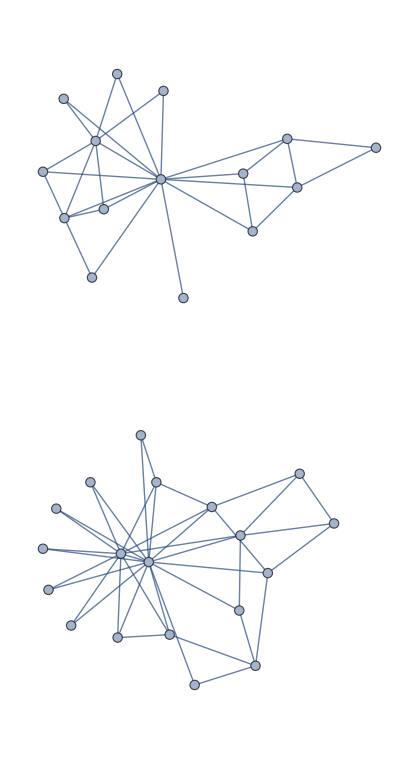

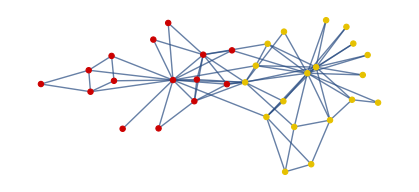

```mathematica
Comm =EdgeDelete[Karate,NextBetweennessEdge[Karate,11]]
HighlightGraph[Karate,Reverse[ConnectedComponents[Comm]]]
```

Ground Truth

-Graphics-

## A dendrogram tree

An hierarchical decomposition.

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
Off[DirectAgglomerate::ties]
```

```mathematica
Manipulate[DendrogramPlot[{1,2,10,4,8, 15,13},LeafLabels->(#&),HighlightLevel->i,Orientation->Left],{{i,None,"Level"},{None,2,3,6}}]
```

Find a betweenness cut

```mathematica
BetweennessCut[g_]:= Module[{graph=g},
While[Length[cc=ConnectedComponents[graph]]<2,
graph= EdgeDelete[graph,TopEdgeBetweennessCentrality[graph]];];
cc]
```

Find a dendrogram with betweenness

```mathematica
BetweennessClusters[g_]:=Module[{graph=g,list={},c,d,e},
If[VertexCount[g]==1,First@VertexList[g],c=BetweennessCut[g];
Cluster[BetweennessClusters[d=Subgraph[g,First@c]],BetweennessClusters[e=Subgraph[g,Last@c]],EdgeCount[g],Length[First@c],Length[Last@c]]]]
```

```mathematica
Cl =BetweennessClusters[Karate];
```

A dendrogram based on edge  betweenness

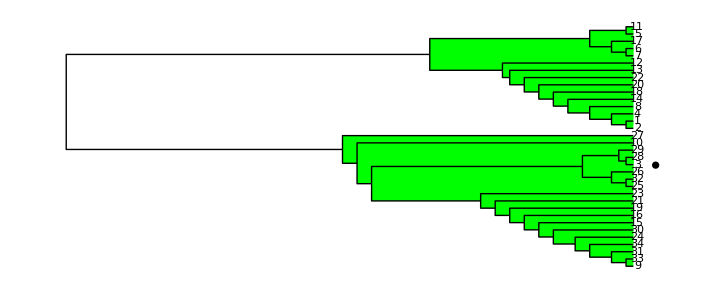

```mathematica
Show[Graphics[Disk[{3,15},.5]],DendrogramPlot[Cl,Orientation->Left,LeafLabels->(#&),HighlightLevel->2]]
```

```mathematica
KarateClub1
```

{3,4,14,2,1,8,22,20,18,13,12,7,17,6,5,11}

## Hierarchical Clustering

Hierarchical decomposition - Bottom up

Combine nodes based on similarity - start with pairs and and increase “cluster” size

Join to groups based on single....

Algorithm:

Choose a similarity measure and evaluate it for all vertex pairs.

Assign each vertex to a group of its own, consisting of just that one vertex. The initial similarities of the groups are simply the similarities of the vertices.

Find the pair of groups with the highest similarity and join them together into a single group.

Calculate the similarity between the new composite group and all others using one of the three methods  (single-, complete-, or average- linkage clustering).

Repeat from step 3 until all vertices have been joined into a single group.

Two similarity example (structural similarity):

Pearson correlation coefficient

r_ij = (cov(A_i,A_j))/(σ_i σ_j)= (∑_k (A_ik-μ_i)(A_jk-μ_j))/(σ_i σ_j)
μ_i =  (∑_k A_ik)/n
σ_i = √(∑_k (A_ik-μ_i)^2)

Cosine Similarity

cos θ = (x·y)/(|x|·|y|)
σ_ij = cos θ = (∑_k A_ik A_jk)/(√(∑_k A_ik^2)√(∑_k A_jk^2))

```mathematica
A=AdjacencyMatrix[Karate];
```

```mathematica
Manipulate[Column[{HighlightGraph[Karate,{VertexList[Karate][[i=First@First@Position[VertexList[Karate],x]]],VertexList[Karate][[j=First@First@Position[VertexList[Karate],y]]]}],Normal[A[[i]]],Normal[A[[j]]],"Perason Correlation: " <> ToString[N[-(Correlation[A[[i]],A[[j]]]-1),4]],"Cosine Similarity: "<> ToString[N[CosineDistance[Normal[A[[i]]],Normal[A[[j]]]],4]]}],{x,VertexList[Karate]},{y,VertexList[Karate]}]
```

## Let’s Check

```mathematica
A=AdjacencyMatrix[Karate];
```

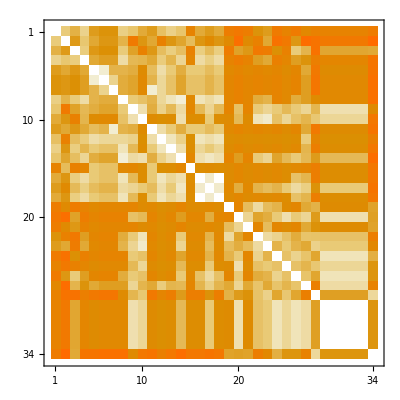

```mathematica
MatrixPlot[-(Correlation[A]-1)]
```

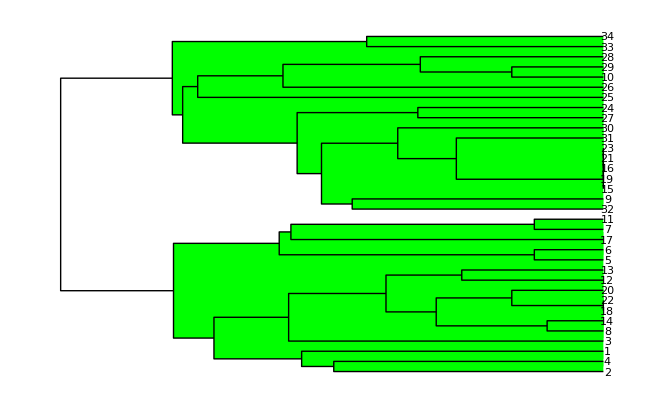

```mathematica
DendrogramPlot[DirectAgglomerate[-(Correlation[A]-1),VertexList[Karate],Linkage->"Average"],LeafLabels->(#&),Orientation->Left,HighlightLevel->3]
```

```mathematica
KarateClub1
```

{3,4,14,2,1,8,22,20,18,13,12,7,17,6,5,11}

```mathematica
CosineDistanceMatrix[A_]:=
Table[Table[CosineDistance[Normal[A[[i]]],Normal[A[[j]]]],{i,1,Length[A]}],{j,1,Length[A]}]
```

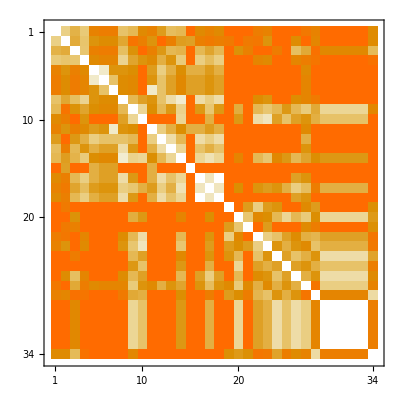

```mathematica
MatrixPlot[CosineDistanceMatrix[A]]
```

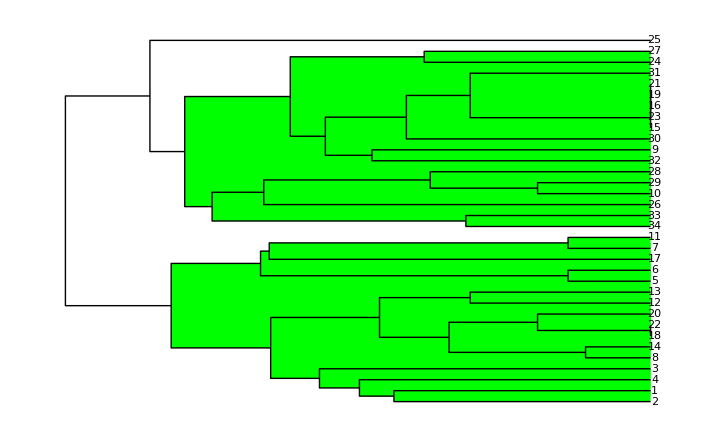

```mathematica
DendrogramPlot[DirectAgglomerate[CosineDistanceMatrix[A],VertexList[Karate],Linkage->"Average"],LeafLabels->(#&),Orientation->Left,HighlightLevel->3]
```

Recall the correct split

## Clique Percolation Method

The clique percolation method builds up the communities from k-cliques, which correspond to complete (fully connected) sub-graphs of k nodes. (E.g., a k-clique at k = 3 is equivalent to a triangle). Two k-cliques are considered adjacent if they share k − 1 nodes. A community is defined as the maximal union of k-cliques that can be reached from each other through a series of adjacent k-cliques. Such communities can be best interpreted with the help of a k-clique template (an object isomorphic to a complete graph of k nodes). Such a template can be placed onto any k-clique in the graph, and rolled to an adjacent k-clique by relocating one of its nodes and keeping its other k − 1 nodes fixed. Thus, the k-clique communities of a network are all those sub-graphs that can be fully explored by rolling a k-clique template in them, but cannot be left by this template.

-Graphics-

## Homework 7

Play around with  “Network of Thrones”. Compare the tribe to community detecting algorithms. What is working best.

Using Mathematica FindGraphCommunities function. What is working the best?

Using  “Edge Betweenness Algorithm” (and Hierarchical Clustering). Does it finds a “good”  dendrogram tree ? Explain/show.

Using  Hierarchical Clustering and a similarity measure Does it finds a “good”  dendrogram tree ? Explain/show.

Using the “Louvain Modularity” method (need to implement it).

Bounus: Playaround with the Facebook network: Find something intresting (you can use all previous units).